Electric Field

28200000/543169

The central frequency is 407.056 THz

The frequency bandwidth is 51.9175 THz

-Graphics-

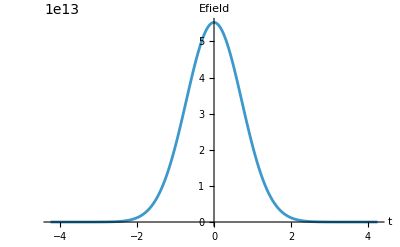

```mathematica
(* parameters*)
ClearAll["Global`*"]

λ = 737*10^(-9); (*m*)
fo = (3*10^(8)/λ)*10^(-12); (*THz*)
ωo = 2*Pi*fo*10^(12); (*rad/s*)
Δλ = 94*10^(-9);  (*m*)
Δf= ((3*10^8)/λ^2*Δλ)*10^(-12) (*Thz*)
Δω = 2*Pi*Δf*10^(12);
Δt = .441/(Δf*10^(12)); (*s*)

A = 1;

tmin=-5*Δt;
tmax=5*Δt;
tmin1=-5*Δt;
tmax1=5*Δt;
ωmin = -5*Δω+ωo;
ωmax = 5*Δω+ωo;

σt = Δt/(2*√(2*Log[2]));
σω = Δω/(2*√(2*Log[2]));

Print["The central frequency is ", N[fo], " THz"]
Print["The frequency bandwidth is ", N[Δf], " THz"]

(* E field in the frequency domain*)
Efieldω[ω_] := A* Exp[-(ω-ωo)^2/(2σω^2)];

(*E field in the time domain Fourier transformed from the frequency domain*)
Efieldt[t_] =∫_(-∞)^∞ (1/(2Pi))Efieldω[w]Exp[-I*w*t]ⅆw;

Plot[Efieldω[ω],{ω,ωmin,ωmax},PlotPoints->500,MaxRecursion->4,PlotRange->All, AxesLabel->{ω, Efield}]
Plot[Abs[Efieldt[t]], {t, tmin1, tmax1}, PlotPoints->500, MaxRecursion->4, PlotRange->All, AxesLabel->{t, Efield}]
```

Sellemeier Equations

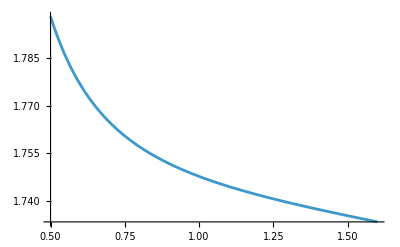

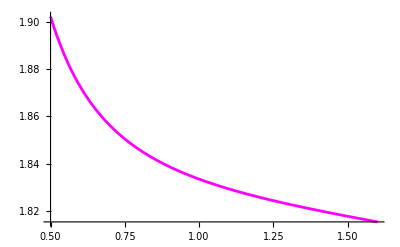

```mathematica
(*Sellemeier Equations for PPKTP*)
(*z axis: https://doi.org/10.1063/1.123408*)(*y axis: https://doi.org/10.1063/1.1668320*)
(*temperature dependence: https://opg.optica.org/ao/fulltext.cfm?uri=ao-42-33-6661*)

(*y*)
A1y = 2.09930;
A2y = 0.922683;
A3y = 0.0467695;
A4y = 0.0138408;

(*z*)
Az = 2.12725;
Bz = 1.18431;
Cz = 5.14852*10^-2;
Dz = 0.6603;
Ez = 100.00507;
Fz = 9.68956*10^-3;

temp = 60;

n1z[λ_] := 9.9587*10^-6 + 9.9228*10^-6/λ + -8.9603*10^-6/(λ^2) + 4.1010*10^-6/(λ^3);
n2z[λ_] := -1.1882*10^-8 + 10.459*10^-8/λ + -9.8136*10^-8/(λ^2) + 3.1481*10^-8/(λ^3);
Δnz[λ_] := n1z[λ]*(temp - 25) + n2z[λ]*(temp - 25)^2;

n1y[λ_] := 6.2897*10^-6 + 6.3061*10^-6/λ + -6.0629*10^-6/(λ^2) + 2.6486*10^-6/(λ^3);
n2y[λ_] := -.14445*10^-8 + 2.2244*10^-8/λ + -3.5770*10^-8/(λ^2) + 1.3470*10^-8/(λ^3);
Δny[λ_] := n1y[λ]*(temp - 25) + n2y[λ]*(temp - 25)^2;

ny[λ_] := Sqrt[A1y + A2y/(1 - A3y/(λ^2)) - A4y*λ^2] + Δny[λ];

nz[λ_] := Sqrt[Az + Bz/(1 - Cz/(λ^2)) + Dz/(1 - Ez/(λ^2)) - Fz*λ^2] + Δnz[λ];

p1 = Plot[ny[λ], {λ, 0.5, 1.6}]
p2 = Plot[nz[λ], {λ, 0.5, 1.6}, PlotStyle -> Magenta]
```

Poling Period

```mathematica
λpo = 520*10^-9; 
λso = 780*10^-9; 
λio = 1/(1/λpo -1/λso);
c = 3*10^8;

Print["The central wavelength for the idler is ", N[λio], "m"]

ωpo = 2π c/λpo;
ωso = 2π c/λso;
ωio = 2π c/λio;

kpo = nz[λpo*10^6]*ωpo/c;
kso = nz[λso*10^6]*ωso/c;
kio = nz[λio*10^6]*ωio/c;

Λ = (-2π/(-kpo + kso +kio))*10^6;
Print["The poling period is ", N[Λ], " microns"]
```

The central wavelength for the idler is 1.56×10^-6m

The poling period is 9.05838 microns

JSI (no cavity)

```mathematica
Clear[λi, λs];

Δt=1*10^-9;
Δν=(.441/Δt) /10^9;
σν=Δν/(2*Sqrt[2*Log[2]]);

λs[ν_]:=c/ν;
λi[ν_]:=c/ν;

L = .5*10^-2;

νso = (c/λso) /10^9;
νio = (c/λio) /10^9;
νpo = (c/λpo) /10^9;

Print["The central frequency for the signal is ", N[νso], " Ghz"];
Print["The central frequency for the idler is ", N[νio], " Ghz"];


Δk0 = -nz[λpo*10^6]*2π *νpo*10^9/c + nz[λso*10^6]*2π *νso*10^9/c + nz[λio*10^6]*2π * νio*10^9/c  + 2π/(Λ*10^-6) ;
Print["Delta k0 is ",N[Δk0]]

 (*next order term*)
dkp = D[2π nz[(c/(νp*10^9))*10^6] (νp*10^9/c), νp] /. νp -> νpo;
dks = D[2π nz[(c/(νs*10^9))*10^6] (νs*10^9/c), νs] /. νs -> νso;
dki = D[2π nz[(c/(νi*10^9))*10^6] (νi*10^9/c), νi] /. νi -> νio;
Δk1[ Δνs_,Δνi_]:=(dkp-dks)*Δνs+(dkp-dki)*Δνi;

Δk[ Δνs_,Δνi_]:= Δk0  + Δk1[ Δνs,Δνi]  ;
α[Δνs_,Δνi_] := A* Exp[-(Δνs + Δνi)^2/(2σν^2)];
ϕ[Δνs_, Δνi_] := Sinc[(Δk[Δνs,Δνi] *L)/2];

JSA[Δνs_,Δνi_] := ϕ[Δνs,Δνi]*α[Δνs, Δνi];
JSI[Δνs_, Δνi_] := JSA[Δνs,Δνi]*Conjugate[JSA[Δνs,Δνi]];

δν = 7;

DensityPlot[α[Δνs,Δνi],{Δνs,-δν,δν},{Δνi,-δν,δν}, PlotPoints->100, PlotRange->All, PlotLabel->"Pump (Detuning)",FrameLabel->{"Signal (GHz)","idler (Ghz)",None,None}]
DensityPlot[ϕ[Δνs,Δνi],{Δνs,-δν,δν},{Δνi,-δν,δν}, PlotPoints->100, PlotRange->All, PlotLabel->"Phasematching (Detuning)",FrameLabel->{"Signal (GHz)","idler (Ghz)",None,None}]
DensityPlot[JSI[Δνs,Δνi],{Δνs,-δν,δν},{Δνi,-δν,δν},PlotPoints->100, PlotRange->All, PlotLabel->"JSI (Detuning)",FrameLabel->{"Signal (GHz)","idler (Ghz)",None,None}]
```

The central frequency for the signal is 384615. Ghz

The central frequency for the idler is 192308. Ghz

Delta k0 is 0.

General::munfl: Exp[-2794.13] is too small to represent as a normalized machine number; precision may be lost.

-Graphics-

-Graphics-

General::munfl: Exp[-2794.13] is too small to represent as a normalized machine number; precision may be lost.

-Graphics-

Cavity Physics

The finesse is 294.566

The spectral width is: 5.51247×10^7 Hz

The spectral width with no loss is: 5.47965×10^7 Hz

The free spectral range is 16.2379 GHz

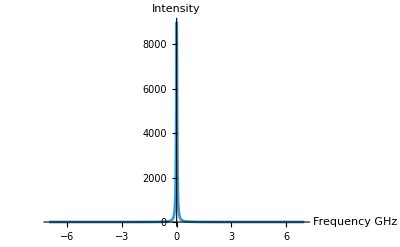

```mathematica
L = .5*10^-2;
λso = 780*10^-9;
(*Reflectivity*)
R1 = .999;
R2 = .98;
r1 = √R1;
r2 = √R2;
(*loss coefficient for absorption for PPKTP at 775 (ppm/cm)*)
αs = 127*10^-6*100;
αr = αs+ 1/(2*L)Log[1/(R1*R2)];
(*αr = .18633;*)

(*Finesse*)
Fnoloss = (π √(r1*r2))/(1-r1*r2);
F = (π*Exp[-αr*L/2])/(1 - Exp[-αr*L]);
Print["The finesse is ", N[F]];
(*Free spectral range*)
νf = (c*10^-9)/(2*L*nz[λso*10^6]);
ng[λ_]:=nz[λ]-λ*nz'[λ];
νfg = (c*10^-9)/(2*L*ng[λso*10^6]);

(*Print["the group index is: ",ng[λso*10^6]];
Print["the normal index is: ", nz[λso*10^6]];
Print["The FSR using group index is: ", νfg, " GHz"];*)

(*Spectral width*)
sw = νf/F;
swnoloss = νf/Fnoloss;
Print["The spectral width is: ", N[sw]*10^9, " Hz"]
Print["The spectral width with no loss is: ", N[swnoloss]*10^9, " Hz"]
(*Internal resonator intensity*)
Io = 1;

Imax = Io/(1-r1*r2)^2;
Print["The free spectral range is ",νf, " GHz"]

Intensity[ Δν_]:= Imax/(1 + ((2*F)/π)^2*(Sin[(π*Δν)/νf])^2);

qso=Round[νso/νf]; (*closest mode to signal*)
νr=qso*νf; (*resonant frequency closest to signal*)
δνr=νr-νso; (*how far apart they are*)

δν2 = 7;

Plot[Intensity[Δν],{Δν,-δν2,δν2},PlotPoints->100,PlotRange->All, AxesLabel->{Frequency(GHz), Intensity}]
```

JSI (cavity)

```mathematica
JSA[Δνs_,Δνi_] := ϕ[Δνs,Δνi]*α[Δνs, Δνi]*Intensity[Δνs-δνr];
JSI[Δνs_, Δνi_] := JSA[Δνs,Δνi]*Conjugate[JSA[Δνs,Δνi]];
DensityPlot[JSI[Δνs,Δνi],{Δνs,-δν2,δν2},{Δνi,-δν2,δν2},PlotPoints->100, PlotRange->All, PlotLabel->"JSI",FrameLabel->{"Signal (GHz)","idler (Ghz)",None,None}]
```

General::munfl: Exp[-2794.13] is too small to represent as a normalized machine number; precision may be lost.

-Graphics-

ABCD Matrices for Hemispherical Cavity

ABCD Matrix: ABCD

The radius of curvature of the beam at the first mirror is -8.22396×10^13

The beam radius at the first mirror is 24.816 microns

The radius of curvature of the beam at the second mirror is 0.958258 cm

The beam radius at the second mirror is 36.7283 microns

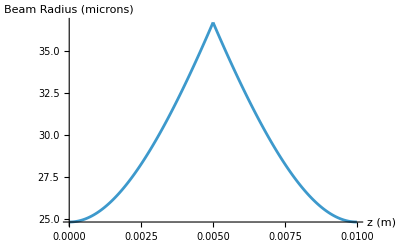

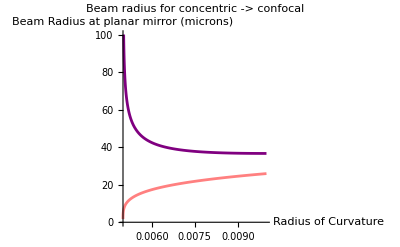

```mathematica
RC = .92*10^-2; (*Radius of curvature*)
λso = 780*10^-9;
L = .5*10^-2;
m1 = {{1,0},{0,1}}; (*flat mirror*)
m2[L_] := {{1,L},{0,1}}; (*propagation*)
m3[RC_]:= {{1,0},{-2/RC,1}}; (*curved mirror as a function of radius of curvature*)

ABCD[RC_,L_] := m1.m2[L].m3[RC].m2[L];
Print["ABCD Matrix: ", ABCD];

mA[RC_,L_] := ABCD[RC,L][[1,1]];
mB[RC_,L_] := ABCD[RC,L][[1,2]];
mC[RC_,L_] := ABCD[RC,L][[2,1]];
mD[RC_,L_] := ABCD[RC,L][[2,2]];

RC1[RC_,L_] := (2*mB[RC,L])/(-(mA[RC,L]-mD[RC,L]));(*Radius of curvature of Gaussian beam at first flat mirror*)
W1[RC_,L_] :=√(λso/(nz[λso*10^6]*π))√(Abs[mB[RC,L]]/(√(1-((mA[RC,L]+mD[RC,L])/2)^2)));(*beam waist at first flat mirror*)
z0[RC_,L_] := (nz[λso*10^6]*π*W1[RC,L]^2)/λso;
RC2[z_,RC_,L_] :=  z(1+(z0[RC,L]/z));
W2[z_,RC_,L_] := W1[RC,L](1+(z/z0[RC,L])^2)^(1/2);
W3[z_,RC_,L_] := W1[RC,L](1+((2L-z)/z0[RC,L])^2)^(1/2); 


Print["The radius of curvature of the beam at the first mirror is ",N[RC1[RC,L]]];
Print["The beam radius at the first mirror is ",N[W1[RC,L]*10^6], " microns"];
Print["The radius of curvature of the beam at the second mirror is ",N[RC2[L,RC,L]*10^2], " cm"];
Print["The beam radius at the second mirror is ",N[W2[L,RC,L]*10^6], " microns"];


trip1 = Plot[W2[z,RC,L]*10^6,{z,0,L},PlotPoints->100,PlotRange->All, AxesLabel->{"z (m)", "Beam Radius (microns)"}];
trip2 = Plot[W3[z,RC,L]*10^6,{z,L,2L},PlotPoints->100,PlotRange->All, AxesLabel->{"z (m)", "Beam Radius (microns)"}];
Show[trip1,trip2]


planar = Plot[W1[rc,L]*10^6,{rc,.50001*10^-2,1*10^-2},PlotPoints->100, AxesLabel->{"Radius of Curvature", "Beam Radius at planar mirror (microns)"},PlotLabel->"Beam radius for concentric -> confocal",PlotStyle->Pink,PlotRange->{0,100}];
curved = Plot[W2[L,rc,L]*10^6,{rc,.50001*10^-2,1*10^-2},PlotPoints->100, AxesLabel->{"Radius of Curvature", "Beam Radius at curved mirror (microns)"},PlotLabel->"Beam radius for concentric -> confocal",PlotStyle->Purple,PlotRange->{0,100}];
Show[planar,curved]
```

Modes

The frequency shift from TEM00 to TEM01 is 8.56895 Ghz

TEM00 resonances: 8.56895 GHz

TEM01 resonance: 17.1379 GHz

TEM10 resonance: 17.1379 GHz

The fsr is 16.2379

0

40

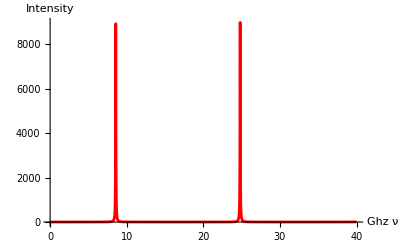

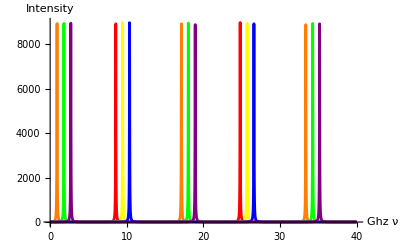

```mathematica
Δζ[RC_,L_]:= 2ArcTan[L/z0[RC,L]];
Δζ2[RC_,L_] := 2ArcCos[√(1-L/RC)];
νHG[q_,z_,m_,RC_,L_]:=q*νf+(z+m+1) Δζ[RC,L]/π νf;
shift [q1_,z1_,m1_,q2_,z2_,m2_,RC_,L_]:= νHG[q2,z2,m2,RC,L] - νHG[q1,z1,m1,RC,L];
Print["The frequency shift from TEM00 to TEM01 is ",shift[1,0,0,1,0,1,RC,L], " Ghz"]

Print["TEM00 resonances: ",νHG[0,0,0,RC,L]," GHz"]
Print["TEM01 resonance: ",νHG[0,1,0,RC,L]," GHz"]
Print["TEM10 resonance: ",νHG[0,0,1,RC,L]," GHz"]

Print["The fsr is ",N[νf]]

left = 0
right = 40
tem00=Plot[Intensity[ν- νHG[0,0,0,RC,L]],{ν,left,right},PlotPoints->100,PlotRange->All,AxesLabel->{ν (Ghz),Intensity},PlotStyle->Red]
tem10=Plot[Intensity[ν-νHG[0,1,0,RC,L]],{ν,left,right},PlotPoints->100,PlotRange->All,AxesLabel->{ν (Ghz),Intensity},PlotStyle->Orange];
tem20=Plot[Intensity[ν-νHG[0,2,0,RC,L]],{ν,left,right},PlotPoints->100,PlotRange->All,AxesLabel->{ν (Ghz),Intensity},PlotStyle->Yellow];
tem30=Plot[Intensity[ν-νHG[0,3,0,RC,L]],{ν,left,right},PlotPoints->100,PlotRange->All,AxesLabel->{ν (Ghz),Intensity},PlotStyle->Green];
tem40=Plot[Intensity[ν-νHG[0,4,0,RC,L]],{ν,left,right},PlotPoints->100,PlotRange->All,AxesLabel->{ν (Ghz),Intensity},PlotStyle->Blue];
tem50=Plot[Intensity[ν-νHG[0,5,0,RC,L]],{ν,left,right},PlotPoints->100,PlotRange->All,AxesLabel->{ν (Ghz),Intensity},PlotStyle->Purple];
Show[tem00,tem10,tem20,tem30, tem40, tem50]
```